```mathematica
2+3
```

5

```mathematica
2*5
```

10

```mathematica
34/2
```

17

```mathematica
sin(2)
```

2 sin

```mathematica
a=Sin[2]
```

Sin[2]

```mathematica
a
```

Sin[2]

```mathematica
a/a^3
```

Csc[2]^2

```mathematica
N[a]
```

0.909297

```mathematica
N[Sin[2],20]
```

0.9092974268256816954

```mathematica
Problem: find an integral of sin(x) in an interval [0.2, 0.9]
```

```mathematica
Integrate[Sin[x],{x,0.2,0.9}]
```

0.358457

```mathematica
∫_0.2^0.9 Sin[x]ⅆx
```

0.358457

```mathematica
Problem: find a derivative  of e^(sin(cos(x^8)))
```

```mathematica
D[ⅇ^Sin[Cos[x^8]],x]
```

-8 ⅇ^Sin[Cos[x^8]] x^7 Cos[Cos[x^8]] Sin[x^8]

```mathematica
Problem: plot this function  e^(sin(cos(x^8)))  on an interval from 0 to 10
```

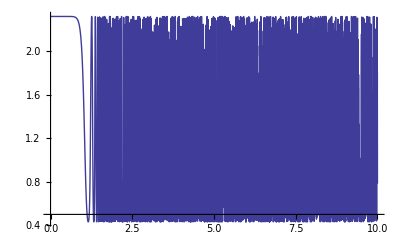

```mathematica
Plot[ⅇ^Sin[Cos[x^8]],{x,0,10}]
```

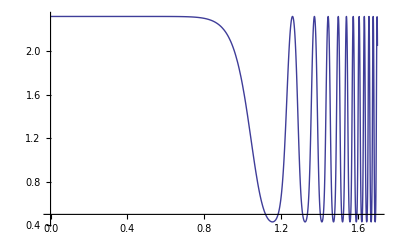

```mathematica
Plot[ⅇ^Sin[Cos[x^8]],{x,0,1.7}]
```

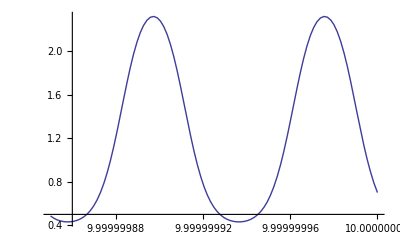

```mathematica
Plot[ⅇ^Sin[Cos[x^8]],{x,9.99999985,10}]
```

```mathematica
Problem: investigate the graph of the derivative of function  e^(sin(cos(x^8)))  on an interval from 0 to 10
```

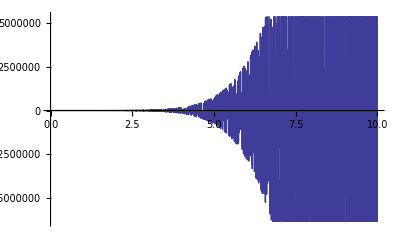

```mathematica
Plot[-8 ⅇ^Sin[Cos[x^8]] x^7 Cos[Cos[x^8]] Sin[x^8],{x,0,10}]
```

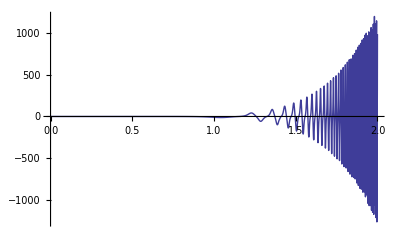

```mathematica
Plot[-8 ⅇ^Sin[Cos[x^8]] x^7 Cos[Cos[x^8]] Sin[x^8],{x,0,2},PlotRange->Full]
```

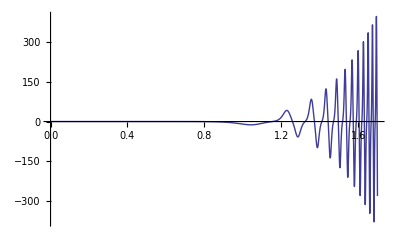

```mathematica
Plot[-8 ⅇ^Sin[Cos[x^8]] x^7 Cos[Cos[x^8]] Sin[x^8],{x,0,1.7},PlotRange->Full]
```